### f_1=a (Npart)^b+c

```mathematica
distr={{10,11},{100,32},{250,54},{500,79},{750,106},{1000,125},{2500,225},{5000,354},{7500,459},{10000,553}};
```

```mathematica
fn1=a*Npart^b+c;
```

```mathematica
FindFit[distr,fn1,{a,b,c},Npart]
```

{a→1.28164,b→0.657873,c→4.96289}

```mathematica
fit1=NonlinearModelFit[distr,fn1,{a,b,c},Npart];Normal[fit2]
```

4.96289+1.28164 Npart^0.657873

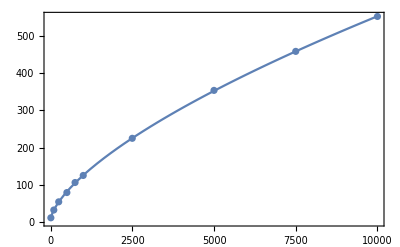

```mathematica
Show[ListPlot[distr],Plot[fit1[Npart],{Npart,0,10000}],Frame->True]
```

Error=1/n∑_(i=1)^n (f_1(i)-d(i))^2:

```mathematica
error1=fit1["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

1.04764